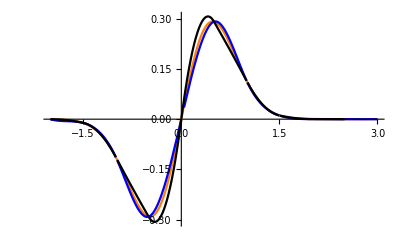

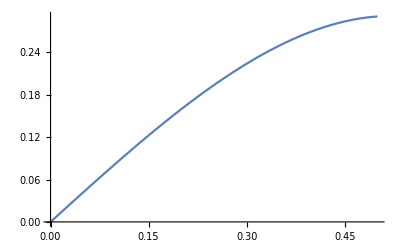

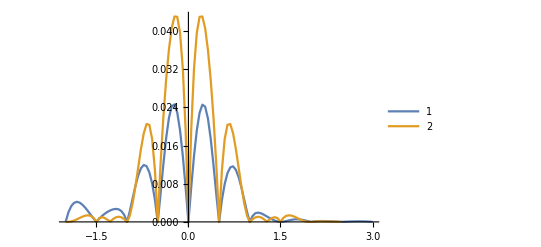

```mathematica
(*,
Plot[-0.000305035+-0.0555624*(x--2)+0.194054*(x--2)^2+-0.252067*(x--2)^3,{x,-2,-1.5}],Plot[-0.0110812+-0.0505589*(x--1.5)+-0.184047*(x--1.5)^2+-0.252067*(x--1.5)^3,{x,-1.5,-1}],Plot[-0.113881+-0.423656*(x--1)+-0.562148*(x--1)^2+1.40367*(x--1)^3,{x,-1,-0.5}],Plot[-0.290786+0.0669525*(x--0.5)+1.54336*(x--0.5)^2+-1.02825*(x--0.5)^3,{x,-0.5,0}],Plot[0+0.83913*(x-0)+0.000990674*(x-0)^2+-1.03221*(x-0)^3,{x,0,0.5}],Plot[0.290786+0.0659619*(x-0.5)+-1.54733*(x-0.5)^2+1.41556*(x-0.5)^3,{x,0.5,1}],Plot[0.113881+-0.419693*(x-1)+0.576017*(x-1)^2+-0.295657*(x-1)^3,{x,1,1.5}],Plot[0.0110812+-0.065419*(x-1.5)+0.132532*(x-1.5)^2+-0.0895967*(x-1.5)^3,{x,1.5,2}],Plot[0.000305035+-8.47177*10^-05*(x-2)+-0.00186325*(x-2)^2+0.00164294*(x-2)^3,{x,2,2.5}],Plot[2.2303*10^-06+-0.000715768*(x-2.5)+0.000601154*(x-2.5)^2+0.00164294*(x-2.5)^3,{x,2.5,3}],
*)
f[x_]:=E^(-2 x^2)*Sin[x];
Splain[x_]:=Piecewise[
{{-0.000305035+-0.0555624*(x--2)+0.194054*(x--2)^2+-0.252067*(x--2)^3,-2≤x≤-1.5},
{-0.0110812+-0.0505589*(x--1.5)+-0.184047*(x--1.5)^2+-0.252067*(x--1.5)^3,-1.5≤x≤-1},
{-0.113881+-0.423656*(x--1)+-0.562148*(x--1)^2+1.40367*(x--1)^3,-1<x≤-0.5},
{-0.290786+0.0669525*(x--0.5)+1.54336*(x--0.5)^2+-1.02825*(x--0.5)^3,-0.5≤x≤0},
{0+0.83913*(x-0)+0.000990674*(x-0)^2+-1.03221*(x-0)^3,0<x<0.5},
{0.290786+0.0659619*(x-0.5)+-1.54733*(x-0.5)^2+1.41556*(x-0.5)^3,0.5≤x≤1},
{0.113881+-0.419693*(x-1)+0.576017*(x-1)^2+-0.295657*(x-1)^3,1≤x≤1.5},
{0.0110812+-0.065419*(x-1.5)+0.132532*(x-1.5)^2+-0.0895967*(x-1.5)^3,1.5≤x≤2},
{0.000305035+-8.47177*10^-05*(x-2)+-0.00186325*(x-2)^2+0.00164294*(x-2)^3,2≤x≤2.5},
{2.2303*10^-06+-0.000715768*(x-2.5)+0.000601154*(x-2.5)^2+0.00164294*(x-2.5)^3,2.5≤x≤3}
}
]
SplineQW[x_]:=Piecewise[{{-0.000305035+-0.000906187*(x--2)+-0.0412922*(x--2)^2,-2≤x≤-1.5},{-0.0110812+-0.0421983*(x--1.5)+-0.326801*(x--1.5)^2,-1.5≤x≤-1},{-0.113881+-0.369*(x--1)+0.0303774*(x--1)^2,-1≤x≤-0.5},{-0.290786+-0.338622*(x--0.5)+1.84039*(x--0.5)^2,-0.5≤x≤0},{0+1.50177*(x-0)+-1.84039*(x-0)^2,0≤x≤0.5},{0.290786+-0.338622*(x-0.5)+-0.0303774*(x-0.5)^2,0.5≤x≤1},{0.113881+-0.369*(x-1)+0.326801*(x-1)^2,1≤x≤1.5},{0.0110812+-0.0421983*(x-1.5)+0.0412922*(x-1.5)^2,1.5≤x≤2},{0.000305035+-0.000906187*(x-2)+0.000601154*(x-2)^2,2≤x≤2.5},{2.2303e-06+-0.000305033*(x-2.5)+0.000601154*(x-2.5)^2,2.5≤x≤3}}];
Show[
Plot[f[x],{x,-2,3},PlotStyle->Orange],
Plot[Splain[x],{x,-2,3},PlotStyle->Blue],
Plot[SplineQW[x],{x,-2,3},PlotStyle->Black],
PlotRange->{{-2,3},{Automatic,Automatic}}
]
Plot[0+0.83913*(x-0)+0.000990674*(x-0)^2+-1.03221*(x-0)^3,{x,0,0.5}]
data=Table[{x//N,Abs[f[x]-Splain[x]]},{x,-2,3,5/110}];
data2=Table[{x//N,Abs[f[x]-SplineQW[x]]},{x,-2,3,5/110}];
ListLinePlot[{data,data2},PlotRange->{{-2,3},{Automatic,Automatic}},PlotLegends->Automatic]
```

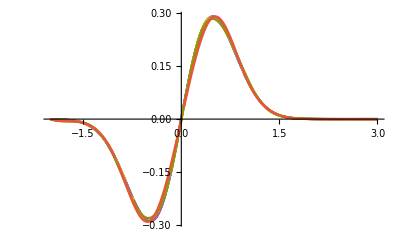

0.0245611

{{11,0.0245611},{12,0.00877682},{13,0.0101356},{14,0.00431466},{15,0.00447779},{17,0.0021469},{18,0.00158256},{19,0.00118146},{20,0.000978709},{21,0.00067238}}

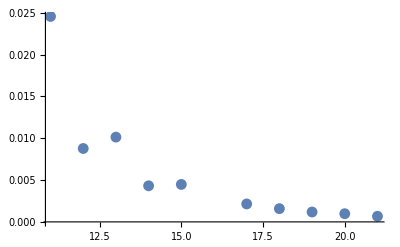

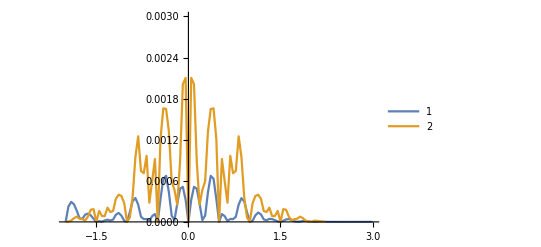

```mathematica
Spline12[x_]:=Piecewise[{{-0.000305035+-0.0667089*(x--2)+0.240541*(x--2)^2+-0.292724*(x--2)^3,-2≤x≤-1.54545},{-0.0084197+-0.0294758*(x--1.54545)+-0.158628*(x--1.54545)^2+-0.292724*(x--1.54545)^3,-1.54545≤x≤-1.09091},{-0.0820831+-0.355124*(x--1.09091)+-0.557797*(x--1.09091)^2+1.00475*(x--1.09091)^3,-1.09091≤x≤-0.636364},{-0.26439+-0.239433*(x--0.636364)+0.812317*(x--0.636364)^2+0.384807*(x--0.636364)^3,-0.636364≤x≤-0.181818},{-0.16925+0.737554*(x--0.181818)+1.33705*(x--0.181818)^2+-2.23742*(x--0.181818)^3,-0.181818≤x≤0.272727},{0.232127+0.566227*(x-0.272727)+-1.71397*(x-0.272727)^2+1.01641*(x-0.272727)^3,0.272727≤x≤0.727273},{0.230831+-0.361926*(x-0.727273)+-0.327965*(x-0.727273)^2+0.618463*(x-0.727273)^3,0.727273≤x≤1.18182},{0.0566406+-0.276731*(x-1.18182)+0.515394*(x-1.18182)^2+-0.347418*(x-1.18182)^3,1.18182≤x≤1.63636},{0.00471256+-0.0235328*(x-1.63636)+0.0416424*(x-1.63636)^2+-0.0264207*(x-1.63636)^3,1.63636≤x≤2.09091},{0.000138362+-0.00205252*(x-2.09091)+0.0056142*(x-2.09091)^2+-0.00387622*(x-2.09091)^3,2.09091≤x≤2.54545},{1.3226*10^-06+0.000648677*(x-2.54545)+0.00032844*(x-2.54545)^2+-0.00387622*(x-2.54545)^3,2.54545≤x≤3}}];
Spline13[x_]:=Piecewise[{{-0.000305035+-0.0527145*(x--2)+0.203327*(x--2)^2+-0.271986*(x--2)^3,-2≤x≤-1.58333},{-0.00664449+-0.0249347*(x--1.58333)+-0.136655*(x--1.58333)^2+-0.271986*(x--1.58333)^3,-1.58333≤x≤-1.16667},{-0.0604338+-0.280474*(x--1.16667)+-0.476638*(x--1.16667)^2+0.535704*(x--1.16667)^3,-1.16667≤x≤-0.75},{-0.221296+-0.39866*(x--0.75)+0.192992*(x--0.75)^2+1.27044*(x--0.75)^3,-0.75≤x≤-0.333333},{-0.261997+0.423857*(x--0.333333)+1.78105*(x--0.333333)^2+-1.95928*(x--0.333333)^3,-0.333333≤x≤0.0833333},{0.0820888+0.887602*(x-0.0833333)+-0.668057*(x-0.0833333)^2+-0.624218*(x-0.0833333)^3,0.0833333≤x≤0.5},{0.290786+0.00577427*(x-0.5)+-1.44833*(x-0.5)^2+1.46637*(x-0.5)^3,0.5≤x≤0.916667},{0.14782+-0.437434*(x-0.916667)+0.384629*(x-0.916667)^2+-0.0631465*(x-0.916667)^3,0.916667≤x≤1.33333},{0.0277639+-0.149798*(x-1.33333)+0.305696*(x-1.33333)^2+-0.224884*(x-1.33333)^3,1.33333≤x≤1.75},{0.00215246+-0.0121788*(x-1.75)+0.0245908*(x-1.75)^2+-0.0176664*(x-1.75)^3,1.75≤x≤2.16667},{6.92324*10^-05+-0.000887751*(x-2.16667)+0.00250779*(x-2.16667)^2+-0.00185061*(x-2.16667)^3,2.16667≤x≤2.58333},{8.46084*10^-07+0.00023821*(x-2.58333)+0.000194522*(x-2.58333)^2+-0.00185061*(x-2.58333)^3,2.58333≤x≤3}}];
Spline14[x_]:=Piecewise[{{-0.000305035+-0.0391709*(x--2)+0.160273*(x--2)^2+-0.2416*(x--2)^3,-2≤x≤-1.61538},{-0.00540771+-0.0231026*(x--1.61538)+-0.118495*(x--1.61538)^2+-0.2416*(x--1.61538)^3,-1.61538≤x≤-1.23077},{-0.0455682+-0.221472*(x--1.23077)+-0.397264*(x--1.23077)^2+0.187831*(x--1.23077)^3,-1.23077≤x≤-0.846154},{-0.17883+-0.443703*(x--0.846154)+-0.180536*(x--0.846154)^2+1.50014*(x--0.846154)^3,-0.846154≤x≤-0.461538},{-0.290839+0.0831672*(x--0.461538)+1.5504*(x--0.461538)^2+-0.816229*(x--0.461538)^3,-0.461538≤x≤-0.0769231},{-0.0759432+0.91355*(x--0.0769231)+0.608596*(x--0.0769231)^2+-2.01834*(x--0.0769231)^3,-0.0769231≤x≤0.307692},{0.250616+0.485987*(x-0.307692)+-1.72026*(x-0.307692)^2+1.08436*(x-0.307692)^3,0.307692≤x≤0.692308},{0.244754+-0.356062*(x-0.692308)+-0.46907*(x-0.692308)^2+0.846346*(x-0.692308)^3,0.692308≤x≤1.07692},{0.0865712+-0.341288*(x-1.07692)+0.507483*(x-1.07692)^2+-0.290182*(x-1.07692)^3,1.07692≤x≤1.46154},{0.013868+-0.079695*(x-1.46154)+0.172658*(x-1.46154)^2+-0.135388*(x-1.46154)^3,1.46154≤x≤1.84615},{0.00105421+-0.00696462*(x-1.84615)+0.016441*(x-1.84615)^2+-0.0135336*(x-1.84615)^3,1.84615≤x≤2.23077},{3.7605*10^-05+-0.000323707*(x-2.23077)+0.00082536*(x-2.23077)^2+-0.000608516*(x-2.23077)^3,2.23077≤x≤2.61538},{5.74874*10^-07+4.11335*10^-05*(x-2.61538)+0.000123226*(x-2.61538)^2+-0.000608516*(x-2.61538)^3,2.61538≤x≤3}}];
Spline15[x_]:=Piecewise[{{-0.000305035+-0.0297767*(x--2)+0.127416*(x--2)^2+-0.215713*(x--2)^3,-2≤x≤-1.64286},{-0.00451406+-0.0213084*(x--1.64286)+-0.103705*(x--1.64286)^2+-0.215713*(x--1.64286)^3,-1.64286≤x≤-1.28571},{-0.0351785+-0.177927*(x--1.28571)+-0.334827*(x--1.28571)^2+-0.0288964*(x--1.28571)^3,-1.28571≤x≤-0.928571},{-0.142748+-0.428146*(x--0.928571)+-0.365787*(x--0.928571)^2+1.33547*(x--0.928571)^3,-0.928571≤x≤-0.571429},{-0.281477+-0.178399*(x--0.571429)+1.06508*(x--0.571429)^2+0.336942*(x--0.571429)^3,-0.571429≤x≤-0.214286},{-0.19399+0.711303*(x--0.214286)+1.42609*(x--0.214286)^2+-2.31083*(x--0.214286)^3,-0.214286≤x≤0.142857},{0.136678+0.845689*(x-0.142857)+-1.04981*(x-0.142857)^2+-0.307753*(x-0.142857)^3,0.142857≤x≤0.5},{0.290786+-0.0219348*(x-0.5)+-1.37954*(x-0.5)^2+1.46933*(x-0.5)^3,0.5≤x≤0.857143},{0.173924+-0.445077*(x-0.857143)+0.194744*(x-0.857143)^2+0.20394*(x-0.857143)^3,0.857143≤x≤1.21429},{0.0490987+-0.227935*(x-1.21429)+0.413252*(x-1.21429)^2+-0.290659*(x-1.21429)^3,1.21429≤x≤1.57143},{0.00716336+-0.0439766*(x-1.57143)+0.101832*(x-1.57143)^2+-0.085512*(x-1.57143)^3,1.57143≤x≤1.92857},{0.000550771+-0.00396107*(x-1.92857)+0.0102117*(x-1.92857)^2+-0.00914826*(x-1.92857)^3,1.92857≤x≤2.28571},{2.18825*10^-05+-0.000167579*(x-2.28571)+0.00041003*(x-2.28571)^2+-0.000305627*(x-2.28571)^3,2.28571≤x≤2.64286},{4.10097*10^-07+8.35048*10^-06*(x-2.64286)+8.25727*10^-05*(x-2.64286)^2+-0.000305627*(x-2.64286)^3,2.64286≤x≤3}}];

Spline17[x_]:=Piecewise[{{-0.000305035+-0.0189104*(x--2)+0.0850954*(x--2)^2+-0.178074*(x--2)^3,-2≤x≤-1.6875},{-0.00333882+-0.0178958*(x--1.6875)+-0.0818486*(x--1.6875)^2+-0.178074*(x--1.6875)^3,-1.6875≤x≤-1.375},{-0.0223587+-0.121221*(x--1.375)+-0.248793*(x--1.375)^2+-0.223517*(x--1.375)^3,-1.375≤x≤-1.0625},{-0.0913576+-0.3422*(x--1.0625)+-0.458339*(x--1.0625)^2+0.713001*(x--1.0625)^3,-1.0625≤x≤-0.75},{-0.221296+-0.419775*(x--0.75)+0.210099*(x--0.75)^2+1.4102*(x--0.75)^3,-0.75≤x≤-0.4375},{-0.288922+0.124681*(x--0.4375)+1.53216*(x--0.4375)^2+-0.671886*(x--0.4375)^3,-0.4375≤x≤-0.125},{-0.120839+0.885438*(x--0.125)+0.902265*(x--0.125)^2+-2.30115*(x--0.125)^3,-0.125≤x≤0.1875},{0.173747+0.77519*(x-0.1875)+-1.25506*(x-0.1875)^2+-0.0866177*(x-0.1875)^3,0.1875≤x≤0.5},{0.290786+-0.0345975*(x-0.5)+-1.33626*(x-0.5)^2+1.45496*(x-0.5)^3,0.5≤x≤0.8125},{0.193882+-0.443505*(x-0.8125)+0.027759*(x-0.8125)^2+0.451754*(x-0.8125)^3,0.8125≤x≤1.125},{0.071784+-0.293806*(x-1.125)+0.451278*(x-1.125)^2+-0.266875*(x-1.125)^3,1.125≤x≤1.4375},{0.0158954+-0.0899429*(x-1.4375)+0.201083*(x-1.4375)^2+-0.172779*(x-1.4375)^3,1.4375≤x≤1.75},{0.00215246+-0.0148851*(x-1.75)+0.0391026*(x-1.75)^2+-0.0374053*(x-1.75)^3,1.75≤x≤2.0625},{0.000177968+-0.00140454*(x-2.0625)+0.00403512*(x-2.0625)^2+-0.00407492*(x-2.0625)^3,2.0625≤x≤2.375},{8.74536*10^-06+-7.642*10^-05*(x-2.375)+0.000214879*(x-2.375)^2+-0.000183984*(x-2.375)^3,2.375≤x≤2.6875},{2.33666*10^-07+3.97801*10^-06*(x-2.6875)+4.23945*10^-05*(x-2.6875)^2+-0.000183984*(x-2.6875)^3,2.6875≤x≤3}}];

Spline18[x_]:=Piecewise[{{-0.000305035+-0.0156016*(x--2)+0.0707505*(x--2)^2+-0.163776*(x--2)^3,-2≤x≤-1.70588},{-0.00294037+-0.0164861*(x--1.70588)+-0.0737578*(x--1.70588)^2+-0.163776*(x--1.70588)^3,-1.70588≤x≤-1.41176},{-0.0183366+-0.102375*(x--1.41176)+-0.218266*(x--1.41176)^2+-0.259408*(x--1.41176)^3,-1.41176≤x≤-1.11765},{-0.0739282+-0.298088*(x--1.11765)+-0.447155*(x--1.11765)^2+0.445324*(x--1.11765)^3,-1.11765≤x≤-0.823529},{-0.188952+-0.445552*(x--0.823529)+-0.0542226*(x--0.823529)^2+1.42955*(x--0.823529)^3,-0.823529≤x≤-0.529412},{-0.288316+-0.106457*(x--0.529412)+1.20714*(x--0.529412)^2+0.255835*(x--0.529412)^3,-0.529412≤x≤-0.235294},{-0.208693+0.670021*(x--0.235294)+1.43288*(x--0.235294)^2+-2.12002*(x--0.235294)^3,-0.235294≤x≤0.0588235},{0.0583842+0.962713*(x-0.0588235)+-0.437727*(x-0.0588235)^2+-1.34564*(x-0.0588235)^3,0.0588235≤x≤0.352941},{0.269433+0.356012*(x-0.352941)+-1.62506*(x-0.352941)^2+1.07585*(x-0.352941)^3,0.352941≤x≤0.647059},{0.260939+-0.320703*(x-0.647059)+-0.675774*(x-0.647059)^2+1.15129*(x-0.647059)^3,0.647059≤x≤0.941176},{0.137448+-0.41944*(x-0.941176)+0.340071*(x-0.941176)^2+0.0444882*(x-0.941176)^3,0.941176≤x≤1.23529},{0.0446334+-0.207852*(x-1.23529)+0.379325*(x-1.23529)^2+-0.276159*(x-1.23529)^3,1.23529≤x≤1.52941},{0.00928777+-0.0563872*(x-1.52941)+0.135656*(x-1.52941)^2+-0.125221*(x-1.52941)^3,1.52941≤x≤1.82353},{0.00125226+-0.00908643*(x-1.82353)+0.0251669*(x-1.82353)^2+-0.025473*(x-1.82353)^3,1.82353≤x≤2.11765},{0.000108747+-0.000893033*(x-2.11765)+0.00269069*(x-2.11765)^2+-0.00286671*(x-2.11765)^3,2.11765≤x≤2.41176},{5.91174*10^-06+-5.42309*10^-05*(x-2.41176)+0.00016124*(x-2.41176)^2+-0.000146415*(x-2.41176)^3,2.41176≤x≤2.70588},{1.84389*10^-07+2.61933*10^-06*(x-2.70588)+3.20507*10^-05*(x-2.70588)^2+-0.000146415*(x-2.70588)^3,2.70588≤x≤3}}];
Spline19[x_]:=Piecewise[{{-0.000305035+-0.013104*(x--2)+0.0592289*(x--2)^2+-0.151522*(x--2)^3,-2≤x≤-1.72222},{-0.00262255+-0.0152736*(x--1.72222)+-0.0670391*(x--1.72222)^2+-0.151522*(x--1.72222)^3,-1.72222≤x≤-1.44444},{-0.0152856+-0.087592*(x--1.44444)+-0.193307*(x--1.44444)^2+-0.275334*(x--1.44444)^3,-1.44444≤x≤-1.16667},{-0.0604338+-0.25872*(x--1.16667)+-0.422752*(x--1.16667)^2+0.235441*(x--1.16667)^3,-1.16667≤x≤-0.888889},{-0.159874+-0.439082*(x--0.888889)+-0.226552*(x--0.888889)^2+1.28073*(x--0.888889)^3,-0.888889≤x≤-0.611111},{-0.271871+-0.268478*(x--0.611111)+0.840726*(x--0.611111)^2+0.913553*(x--0.611111)^3,-0.611111≤x≤-0.333333},{-0.261997+0.410063*(x--0.333333)+1.60202*(x--0.333333)^2+-1.43268*(x--0.333333)^3,-0.333333≤x≤-0.0555556},{-0.0551853+0.968436*(x--0.0555556)+0.408124*(x--0.0555556)^2+-2.12963*(x--0.0555556)^3,-0.0555556≤x≤0.222222},{0.19967+0.702202*(x-0.222222)+-1.36657*(x-0.222222)^2+0.0701936*(x-0.222222)^3,0.222222≤x≤0.5},{0.290786+-0.0407523*(x-0.5)+-1.30807*(x-0.5)^2+1.43399*(x-0.5)^3,0.5≤x≤0.777778},{0.20927+-0.435516*(x-0.777778)+-0.113077*(x-0.777778)^2+0.660193*(x-0.777778)^3,0.777778≤x≤1.05556},{0.0937187+-0.345514*(x-1.05556)+0.437083*(x-1.05556)^2+-0.172827*(x-1.05556)^3,1.05556≤x≤1.33333},{0.0277639+-0.142696*(x-1.33333)+0.293061*(x-1.33333)^2+-0.241622*(x-1.33333)^3,1.33333≤x≤1.61111},{0.00555992+-0.035816*(x-1.61111)+0.0917087*(x-1.61111)^2+-0.0901012*(x-1.61111)^3,1.61111≤x≤1.88889},{0.00075615+-0.00572346*(x-1.88889)+0.0166244*(x-1.88889)^2+-0.0177205*(x-1.88889)^3,1.88889≤x≤2.16667},{6.92324*10^-05+-0.00058967*(x-2.16667)+0.00185728*(x-2.16667)^2+-0.00208082*(x-2.16667)^3,2.16667≤x≤2.44444},{4.14449*10^-06+-3.95197*10^-05*(x-2.44444)+0.000123264*(x-2.44444)^2+-0.000117989*(x-2.44444)^3,2.44444≤x≤2.72222},{1.48977*10^-07+1.6479*10^-06*(x-2.72222)+2.49395*10^-05*(x-2.72222)^2+-0.000117989*(x-2.72222)^3,2.72222≤x≤3}}];
Spline20[x_]:=Piecewise[{{-0.000305035+-0.0111848*(x--2)+0.0498449*(x--2)^2+-0.140922*(x--2)^3,-2≤x≤-1.73684},{-0.00236473+-0.0142281*(x--1.73684)+-0.0614095*(x--1.73684)^2+-0.140922*(x--1.73684)^3,-1.73684≤x≤-1.47368},{-0.0129299+-0.0758263*(x--1.47368)+-0.172664*(x--1.47368)^2+-0.279307*(x--1.47368)^3,-1.47368≤x≤-1.21053},{-0.0499317+-0.22473*(x--1.21053)+-0.39317*(x--1.21053)^2+0.078188*(x--1.21053)^3,-1.21053≤x≤-0.947368},{-0.134874+-0.415417*(x--0.947368)+-0.331442*(x--0.947368)^2+1.06059*(x--0.947368)^3,-0.947368≤x≤-0.684211},{-0.247819+-0.369516*(x--0.684211)+0.505865*(x--0.684211)^2+1.27963*(x--0.684211)^3,-0.684211≤x≤-0.421053},{-0.286708+0.162579*(x--0.421053)+1.5161*(x--0.421053)^2+-0.58499*(x--0.421053)^3,-0.421053≤x≤-0.157895},{-0.149592+0.838991*(x--0.157895)+1.05427*(x--0.157895)^2+-2.27387*(x--0.157895)^3,-0.157895≤x≤0.105263},{0.102766+0.921456*(x-0.105263)+-0.740898*(x-0.105263)^2+-1.06581*(x-0.105263)^3,0.105263≤x≤0.368421},{0.274522+0.310082*(x-0.368421)+-1.58232*(x-0.368421)^2+1.0611*(x-0.368421)^3,0.368421≤x≤0.631579},{0.265881+-0.302271*(x-0.631579)+-0.744616*(x-0.631579)^2+1.23702*(x-0.631579)^3,0.631579≤x≤0.894737},{0.157314+-0.437176*(x-0.894737)+0.231976*(x-0.894737)^2+0.240248*(x-0.894737)^3,0.894737≤x≤1.15789},{0.0627107+-0.26517*(x-1.15789)+0.421646*(x-1.15789)^2+-0.258293*(x-1.15789)^3,1.15789≤x≤1.42105},{0.0174218+-0.0969133*(x-1.42105)+0.21773*(x-1.42105)^2+-0.196526*(x-1.42105)^3,1.42105≤x≤1.68421},{0.00341501+-0.0231479*(x-1.68421)+0.0625782*(x-1.68421)^2+-0.0649941*(x-1.68421)^3,1.68421≤x≤1.94737},{0.000472661+-0.00371492*(x-1.94737)+0.0112671*(x-1.94737)^2+-0.0125991*(x-1.94737)^3,1.94737≤x≤2.21053},{4.57106*10^-05+-0.000402412*(x-2.21053)+0.00132044*(x-2.21053)^2+-0.00155053*(x-2.21053)^3,2.21053≤x≤2.47368},{2.99874*10^-06+-2.95753*10^-05*(x-2.47368)+9.63403*10^-05*(x-2.47368)^2+-9.68334*10^-05*(x-2.47368)^3,2.47368≤x≤2.73684},{1.2282*10^-07+1.0124*10^-06*(x-2.73684)+1.98929*10^-05*(x-2.73684)^2+-9.68334*10^-05*(x-2.73684)^3,2.73684≤x≤3}}];
Spline21[x_]:=Piecewise[{{-0.000305035+-0.00968913*(x--2)+0.0421217*(x--2)^2+-0.131696*(x--2)^3,-2≤x≤-1.75},{-0.00215246+-0.0133213*(x--1.75)+-0.0566503*(x--1.75)^2+-0.131696*(x--1.75)^3,-1.75≤x≤-1.5},{-0.0110812+-0.0663394*(x--1.5)+-0.155422*(x--1.5)^2+-0.276196*(x--1.5)^3,-1.5≤x≤-1.25},{-0.0416955+-0.195837*(x--1.25)+-0.362569*(x--1.25)^2+-0.0361807*(x--1.25)^3,-1.25≤x≤-1},{-0.113881+-0.383906*(x--1)+-0.389705*(x--1)^2+0.826755*(x--1)^3,-1≤x≤-0.75},{-0.221296+-0.423742*(x--0.75)+0.230361*(x--0.75)^2+1.41103*(x--0.75)^3,-0.75≤x≤-0.5},{-0.290786+-0.0439935*(x--0.5)+1.28863*(x--0.5)^2+0.186361*(x--0.5)^3,-0.5≤x≤-0.25},{-0.218333+0.635266*(x--0.25)+1.4284*(x--0.25)^2+-1.90454*(x--0.25)^3,-0.25≤x≤0},{0+0.992367*(x-0)+1.32717*10^-06*(x-0)^2+-1.90455*(x-0)^3,0≤x≤0.25},{0.218333+0.635265*(x-0.25)+-1.42841*(x-0.25)^2+0.186393*(x-0.25)^3,0.25≤x≤0.5},{0.290786+-0.0439908*(x-0.5)+-1.28861*(x-0.5)^2+1.41091*(x-0.5)^3,0.5≤x≤0.75},{0.221296+-0.423752*(x-0.75)+-0.23043*(x-0.75)^2+0.82719*(x-0.75)^3,0.75≤x≤1},{0.113881+-0.383869*(x-1)+0.389962*(x-1)^2+-0.0378051*(x-1)^3,1≤x≤1.25},{0.0416955+-0.195976*(x-1.25)+0.361609*(x-1.25)^2+-0.270134*(x-1.25)^3,1.25≤x≤1.5},{0.0110812+-0.0658218*(x-1.5)+0.159008*(x-1.5)^2+-0.154322*(x-1.5)^3,1.5≤x≤1.75},{0.00215246+-0.015253*(x-1.75)+0.043267*(x-1.75)^2+-0.0472559*(x-1.75)^3,1.75≤x≤2},{0.000305035+-0.00247993*(x-2)+0.00782512*(x-2)^2+-0.0091488*(x-2)^3,2≤x≤2.25},{3.11737*10^-05+-0.000282766*(x-2.25)+0.000963522*(x-2.25)^2+-0.00118221*(x-2.25)^3,2.25≤x≤2.5},{2.2303*10^-06+-2.26701*10^-05*(x-2.5)+7.68609*10^-05*(x-2.5)^2+-8.08664*10^-05*(x-2.5)^3,2.5≤x≤2.75},{1.03032*10^-07+5.97854*10^-07*(x-2.75)+1.62111*10^-05*(x-2.75)^2+-8.08664*10^-05*(x-2.75)^3,2.75≤x≤3}}];
Show[
Plot[{f[x],Spline21[x],Spline20[x],Spline19[x],Spline18[x],Spline17[x],Spline15[x],Spline14[x],Spline13[x],Spline12[x],Splain[x]},{x,-2,3}]
]
Max[Table[f[x]-Splain[x],{x,-2,3,5/110}]]
data={
{11,Max[Table[f[x]-Splain[x],{x,-2,3,5/110}]]},
{12,Max[Table[f[x]-Spline12[x],{x,-2,3,5/110}]]},
{13,Max[Table[f[x]-Spline13[x],{x,-2,3,5/110}]]},
{14,Max[Table[f[x]-Spline14[x],{x,-2,3,5/110}]]},
{15,Max[Table[f[x]-Spline15[x],{x,-2,3,5/110}]]},
{17,Max[Table[f[x]-Spline17[x],{x,-2,3,5/110}]]},
{18,Max[Table[f[x]-Spline18[x],{x,-2,3,5/110}]]},
{19,Max[Table[f[x]-Spline19[x],{x,-2,3,5/110}]]},
{20,Max[Table[f[x]-Spline20[x],{x,-2,3,5/110}]]},
{21,Max[Table[f[x]-Spline21[x],{x,-2,3,5/110}]]}
}
ListPlot[data]

SplineQW21[x_]:=Piecewise[{{-0.000305035+-0.00197191*(x--2)+-0.0216712*(x--2)^2,-2≤x≤-1.75},{-0.00215246+-0.0128075*(x--1.75)+-0.0916293*(x--1.75)^2,-1.75≤x≤-1.5},{-0.0110812+-0.0586222*(x--1.5)+-0.25534*(x--1.5)^2,-1.5≤x≤-1.25},{-0.0416955+-0.186292*(x--1.25)+-0.409795*(x--1.25)^2,-1.25≤x≤-1},{-0.113881+-0.39119*(x--1)+-0.153881*(x--1)^2,-1≤x≤-0.75},{-0.221296+-0.46813*(x--0.75)+0.760672*(x--0.75)^2,-0.75≤x≤-0.5},{-0.290786+-0.0877944*(x--0.5)+1.51043*(x--0.5)^2,-0.5≤x≤-0.25},{-0.218333+0.667419*(x--0.25)+0.823656*(x--0.25)^2,-0.25≤x≤0},{0+1.07925*(x-0)+-0.823656*(x-0)^2,0≤x≤0.25},{0.218333+0.667419*(x-0.25)+-1.51043*(x-0.25)^2,0.25≤x≤0.5},{0.290786+-0.0877944*(x-0.5)+-0.760672*(x-0.5)^2,0.5≤x≤0.75},{0.221296+-0.46813*(x-0.75)+0.153881*(x-0.75)^2,0.75≤x≤1},{0.113881+-0.39119*(x-1)+0.409795*(x-1)^2,1≤x≤1.25},{0.0416955+-0.186292*(x-1.25)+0.25534*(x-1.25)^2,1.25≤x≤1.5},{0.0110812+-0.0586222*(x-1.5)+0.0916293*(x-1.5)^2,1.5≤x≤1.75},{0.00215246+-0.0128075*(x-1.75)+0.0216712*(x-1.75)^2,1.75≤x≤2},{0.000305035+-0.00197191*(x-2)+0.00350584*(x-2)^2,2≤x≤2.25},{3.11737e-05+-0.000218986*(x-2.25)+0.000412848*(x-2.25)^2,2.25≤x≤2.5},{2.2303e-06+-1.25618e-05*(x-2.5)+1.62111e-05*(x-2.5)^2,2.5≤x≤2.75},{1.03032e-07+-4.4563e-06*(x-2.75)+1.62111e-05*(x-2.75)^2,2.75≤x≤3}}];
data3=Table[{x//N,Abs[f[x]-Spline21[x]]},{x,-2,3,5/110}];
data4=Table[{x//N,Abs[f[x]-SplineQW21[x]]},{x,-2,3,5/110}];
ListLinePlot[{data3,data4},PlotRange->{{-2,3},{Automatic,0.003}},PlotLegends->Automatic]
```